# Hadamard _s Ū of the BPT Green function in ℳ_2

Copyright (c) 2026 David Q. Aruquipa, Marc Casals and Brien Nolan

This notebook is based on the supplemental material provided in PRD 100, 104037 (2019). Besides the calculation of Synge’s world function σ̄ in ℳ_2, we also provide a small coordinate expansion for the biscalar _s Ū, which satisfies the transport equation

(2(σ̄)^i∇_i + □σ̄ - 2 + 2s a^i(σ̄)_i)_s Ū=0

## Spacetime

ⅆ s^2=-f[r]/r^2ⅆ t^2+1/(f[r]r^2)ⅆ r^2

```mathematica
nMax=22; (* order for σ̄ *)
f[r_]=1-(2M)/r;
Subscript[g, t,t][r_]=-f[r]/r^2;
Subscript[g, r,r][r_]=1/(f[r] r^2);
sqrtDetG[r_]=1/r^2;
```

dt = t - t'
dr = r - r'

### Small coordinate expansion for σ̄

```mathematica
Clear@σCoefγ
σCoefγ[0,0][r_]=0; 
σCoefγ[2,0][r_]=(Subscript[g, t,t][r])/2;
σCoefγ[0,2][r_]=(Subscript[g, r,r][r])/2;
Do[σCoefγ[2i+1,_][r_]=0,{i,0,nMax/2}];
```

```mathematica
σExp=0;
σExtra=0;
nCurrent=2;
Do[If[i+k>= 2 && i+k<=nCurrent,σExp=σExp+σCoefγ[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,nCurrent},{k,0,nCurrent}];
σSumt=1/ϵ D[σExp, dt];(* Subscript[σ̄, t]=(∂σ̄)/(∂dt)ⅆdt/ⅆt=1/ϵ(∂σ̄)/(∂dt), the 1/ϵ corrects the order in Subscript[σ̄, t] (differentiation reduces the order of the expansion) *)
σSumr=D[σExp, r]+1/ϵ D[σExp, dr]; (* Subscript[σ̄, r]=(∂σ̄)/(∂r)+(∂σ̄)/(∂dr)ⅆr/ⅆdr=(∂σ̄)/(∂r)+1/ϵ(∂σ̄)/(∂dr), the 1/ϵ corrects the order in Subscript[σ̄, t] (differentiation reduces the order of the expansion) *)
```

```mathematica
(* Solving (σ̄)^i Subscript[σ̄, i]=2 σ̄ *)

While[nCurrent<nMax,
nCurrent=nCurrent+1;
σExtra=0;
Do[If[i+k>= 2 && i+k==nCurrent,σExtra=σExtra+σCoefγ[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,nCurrent},{k,0,nCurrent}];
σExp=σExp+σExtra;
σSumt=σSumt+1/ϵ D[σExtra, dt];
σSumr=σSumr+D[σExtra, r]+1/ϵ D[σExtra, dr];
σEqn=Coefficient[1/(Subscript[g, t,t][r]) Series[σSumt^2,{ϵ,0,nMax}]+1/(Subscript[g, r,r][r]) Series[σSumr^2,{ϵ,0,nMax}]-2 σExp,ϵ,nCurrent];
Print[nCurrent,"\t",Timing[Do[tmp=σCoefγ[i,nCurrent-i][r]/.Solve[Coefficient[σEqn,dt^i dr^(nCurrent-i)]==0,σCoefγ[i,nCurrent-i][r]][[1]];
σCoefγ[i,nCurrent-i][r_]=Simplify[tmp]
,{i,0,nCurrent,2}]][[1]],"\t",Floor[MemoryInUse[]/1024]];];
```

3	0.00704	159231

4	0.015618	158928

5	0.016765	158850

6	0.035677	158500

7	0.081417	158200

8	0.157762	157847

9	0.374399	157700

10	0.606846	157708

11	1.30128	157827

12	2.10476	157434

```mathematica
σ=σExp;
Subscript[σ, t]=1/ϵ D[σ, dt];
Subscript[σ, r]=D[σ, r]+1/ϵ D[σ, dr];
```

```mathematica
Boxσ=1/(Subscript[g, t,t][r])1/ϵ^2 D[σ, dt,dt]+With[{tmp=sqrtDetG[r]/(Subscript[g, r,r][r]) Subscript[σ, r]},1/sqrtDetG[r](D[tmp, r]+1/ϵ D[tmp, dr])];
```

```mathematica
Boxσ+O[ϵ]^2
```

2+O[ϵ]^2

### Small coordinate expansion for _s Ū

```mathematica
(* Solving Subscript[(2(σ̄)^i∇_i + □σ̄ - 2 + 2 s a^i Subscript[σ̄, i]), s] Ū=0 *)

sUNMax=nMax-2; (* order for _s Ū *)
Clear[sUCoef]

sUCoef[i_,_][r_]/;i>sUNMax=0;
sUCoef[0,0][r_]=1;

at=-r/f[r](1-(3M)/r);
ar=r-M;

sUExp=Module[{U0Sum=0},Do[If[i+k>=0 && i+k<=sUNMax,U0Sum=U0Sum+sUCoef[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,sUNMax},{k,0,sUNMax}];U0Sum];
Clear@sUEqns
sUEqns=CoefficientList[
1/(Subscript[g, t,t][r]) Series[1/ϵ Subscript[σ, t] D[sUExp, dt],{ϵ,0,sUNMax}]
+1/(Subscript[g, r,r][r])Series[Subscript[σ, r] (D[sUExp, r]+1/ϵ D[sUExp, dr]),{ϵ,0,sUNMax}]
+1/2 Series[(Boxσ-2 + 2s at Subscript[σ, t] + 2 s ar Subscript[σ, r])sUExp,{ϵ,0,sUNMax}],
ϵ
];
```

```mathematica
Monitor[
Do[
Do[
tmp=sUCoef[i,order-i][r]/.Solve[Coefficient[sUEqns[[order+1]],dt^i dr^(order-i)]==0,sUCoef[i,order-i][r]][[1]];
sUCoef[i,order-i][r_]=Simplify[tmp,Assumptions->{s∈Integers,M>1,r>2M}],
{i,0,order}
],
{order,1,sUNMax}
]
,
{i,order}
]
```

```mathematica
sU=Module[{U0Sum=0},Do[If[i+k>= 0 && i+k<=sUNMax,U0Sum=U0Sum+sUCoef[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,sUNMax},{k,0,sUNMax}];U0Sum];
```

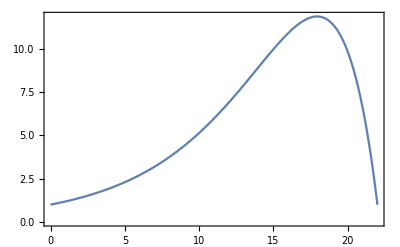

```mathematica
Block[{U,sU10,s=-2,dr=0,r=6,M=1},
U=sU/.{ϵ->1};
Plot[{U},{dt,0,22},Frame->True]
]
```

## Load from file

```mathematica
σ[r_,dr_,dt_]=Block[{σSum,nmax=20},
Get[FileNameJoin[{NotebookDirectory[],"sigma_2d_t_r_nmax"<>ToString@nmax<>".m"}]];
σSum
];
```

cn spacetime: σ as an expansion in dt^{i} dr^k nmax=20

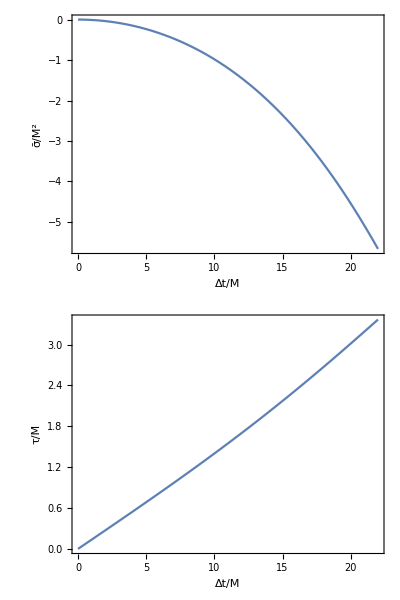

```mathematica
Block[{σFunc,dr=0,r,M=1},
r=6M;
σFunc=σ[r,dr,dt]/.{ϵ->1};
Grid[{
{Plot[{σFunc},{dt,0,22},FrameLabel->{"Δt/M","σ̄/M^2"},Frame->True,ImageSize->Medium]},
{Plot[{√(-2σFunc)},{dt,0,22},FrameLabel->{"Δt/M","τ/M"},Frame->True,ImageSize->Medium]}
}]
]
```

```mathematica
Clear@sU
Subscript[sU, s_][r_,dr_,dt_,M_]=Block[{U0nmax,U},
U0nmax=20;
Get[FileNameJoin[{NotebookDirectory[],"sU_2d_t_r_nmax"<>ToString@U0nmax<>".m"}]];
U=0;
Do[If[i+k>= 0 && i+k<=U0nmax,U=U+U0coef[i,k][r]ϵ^(i+k ) dt^i dr^k],{i,0,U0nmax},{k,0,U0nmax}];
U/.{ϵ->1}
];
```

cn spacetime: BPT Hadamard sU as an expansion in dt  dr  nmax=20

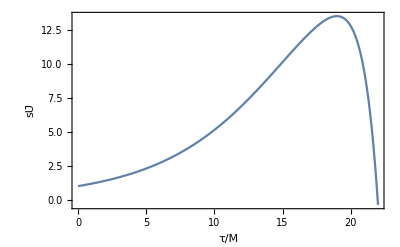

```mathematica
Block[{U,s=-2,dr=0,r=6,M=1},
U=Subscript[sU, s][r,dr,dt,M];
Plot[{U},{dt,0,22},Frame->True,FrameLabel->{"τ/M","sŪ"}]
]
```

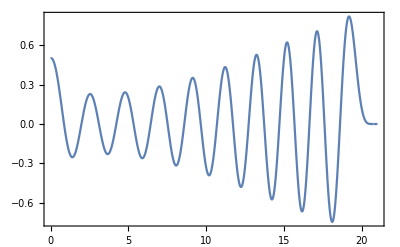

```mathematica
(* Plot of 1/(4π)_s Subscript[G, l]^d(r,r') *)
Block[{mode,U0nmax,s=-2,l=20,M=1,r,τ,U,dr=0,θ=HeavisideTheta,P=JacobiP},
r=6M;
τ=√(-2σ[r,dr,dt])/.{ϵ->1};
U=Subscript[sU, s][r,dr,dt,M]/.{ϵ->1};
mode[dt_]=1/2 θ[τ]θ[π-τ]U √Sinc[τ](Cos[τ/2])^Abs[2s] P[l-Abs[s],0,Abs[2s],Cos[τ]];
Plot[mode[dt],{dt,0,21M},Frame->True]
]
```

```mathematica
(* Expansion of 1/(4π)_s Subscript[G, l]^d(r,r') *)
Block[{mode,U0nmax,τ,U,dr=0,θ=HeavisideTheta,P=JacobiP},
τ=√(-2σ[r,dr,dt])/.{ϵ->1};
U=Subscript[sU, s][r,dr,dt,M]/.{ϵ->1};
mode[dt_]= 1/2 U √Sinc[τ](Cos[τ/2])^Abs[2s] P[l-Abs[s],0,Abs[2s],Cos[τ]];
FullSimplify[Series[mode[dt],{dt,0,5}],Assumptions->{M>0,r>2M,s∈Integers,l∈}]
]
```

1/2+((3 M-r) s dt)/(2 r^2)+((2 M r (-1+l+l^2-7 s^2)-r^2 (l+l^2-3 s^2)+2 M^2 (2+9 s^2)) dt^2)/(8 r^4)+(((12 M+(-1+3 l (1+l)) r) (6 M^2-5 M r+r^2) s+(3 M-r) (18 M^2-18 M r+5 r^2) s^3) dt^3)/(24 r^6)+1/(384 r^8)(r^4 (3 (-1+l) l (1+l) (2+l)-5 (-5+6 l (1+l)) s^2+35 s^4)-4 M r^3 (6+l (1+l) (-16+3 l (1+l))+87 s^2-54 l (1+l) s^2+75 s^4)+4 M^2 r^2 (50+l (1+l) (-47+3 l (1+l))+422 s^2-132 l (1+l) s^2+237 s^4)+216 M^4 (2+3 s^2 (4+s^2))+8 M^3 r (21 l (1+l)+54 l (1+l) s^2-162 s^4-5 (13+87 s^2))) dt^4+1/(1920 r^10)(3 M-r) s (24 M^3 r (-259+55 l+55 l^2+5 (-73+6 l (1+l)) s^2-66 s^4)+24 M^4 (208+240 s^2+27 s^4)-4 M r^3 (92+5 l (1+l) (-26+3 l (1+l))+305 s^2-110 l (1+l) s^2+119 s^4)+4 M^2 r^2 (637+15 l (1+l) (-25+l+l^2)+1240 s^2-240 l (1+l) s^2+333 s^4)+r^4 (5 l (1+l) (-10+3 l (1+l))-70 l (1+l) s^2+63 s^4+3 (4+35 s^2))) dt^5+O[dt]^6

```mathematica
(* 1/(4π)∂/(∂r)_s Subscript[G, l]^d(r,r') *)
D[(1/2 U[r] √Sinc[τ[r]] Cos[τ[r]/2]^Abs[2s] JacobiP[l-Abs[s],0,Abs[2s],Cos[τ[r]]]), r]/.{
U[r]->U,
U'[r]->δU,
τ[r]->τ,
τ'[r]->δτ
}
```

(U δτ Cos[τ/2]^(2 Abs[s]) JacobiP[l-Abs[s],0,2 Abs[s],Cos[τ]] (Cos[τ]/τ-Sin[τ]/τ^2))/(4 √Sinc[τ])+1/2 δU Cos[τ/2]^(2 Abs[s]) JacobiP[l-Abs[s],0,2 Abs[s],Cos[τ]] √Sinc[τ]-1/2 U δτ Abs[s] Cos[τ/2]^(-1+2 Abs[s]) JacobiP[l-Abs[s],0,2 Abs[s],Cos[τ]] Sin[τ/2] √Sinc[τ]-1/4 U δτ (1+l+Abs[s]) Cos[τ/2]^(2 Abs[s]) JacobiP[-1+l-Abs[s],1,1+2 Abs[s],Cos[τ]] Sin[τ] √Sinc[τ]

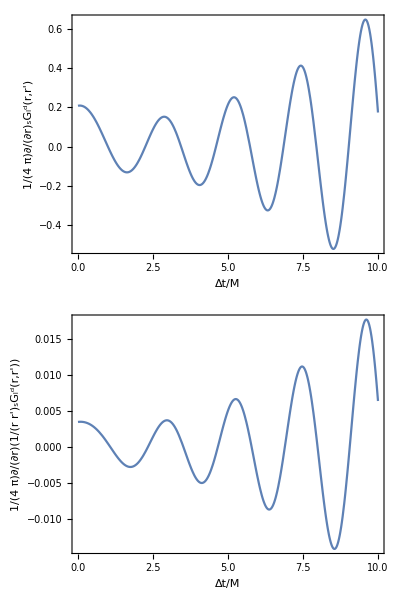

```mathematica
(* Plot of 1/(4π)∂/(∂r)_s Subscript[G, l]^d(r,r') *)
Block[{mode,δMode,δModeNonSym,fullδMode,U0nmax,s=-2,l=20,M=1,rValue,τ,τSymmetric,δτ,U,δU,θ=HeavisideTheta,P=JacobiP},
rValue=6M;
τ=√(-2σ[rValue,0,dt])/.{ϵ->1};
τSymmetric=1/2(√(-2σ[r,r-rp,dt])+√(-2σ[rp,rp-r,-dt]))/.{ϵ->1,rp->rValue};
δτ=(∂_r (*√(-2σ[r,r-rValue,dt])*)τSymmetric)/.{ϵ->1,r->rValue,rp->rValue};

U=Subscript[sU, s][rValue,0,dt,M]/.{ϵ->1};

δU=(D[Subscript[sU, s][r,r-rValue,dt,M], r])/.{r->rValue};

δMode[dt_]=(U ((δτ Cos[τ/2]^(2 Abs[s]) JacobiP[l-Abs[s],0,Abs[2s],Cos[τ]] (Cos[τ]/τ-Sin[τ]/τ^2))/(4 √Sinc[τ])-1/2 δτ Abs[s] Cos[τ/2]^(-1+Abs[2s]) P[l-Abs[s],0,Abs[2s],Cos[τ]] Sin[τ/2] √Sinc[τ]-1/4 δτ (1+l+Abs[s]) Cos[τ/2]^Abs[2s] P[-1+l-Abs[s],1,1+Abs[2s],Cos[τ]] Sin[τ] √Sinc[τ])+1/2 δU Cos[τ/2]^Abs[2s] P[l-Abs[s],0,Abs[2s],Cos[τ]] √Sinc[τ])θ[τ]θ[π-τ];
mode[dt_]=1/2 U √Sinc[τ](Cos[τ/2])^Abs[2s] P[l-Abs[s],0,Abs[2s],Cos[τ]]θ[τ]θ[π-τ];
fullδMode[δM_,dt_]=δMode[dt]/rValue^2-mode[dt]/rValue^3;

Grid[{
{Plot[δMode[dt],{dt,0,10M},Frame->True,ImageSize->Medium,FrameLabel->{"Δt/M","1/(4  π)∂/(∂r)_sG_l^d(r,r')"}]},
{Plot[fullδMode[δMode,dt],{dt,0,10M},Frame->True,ImageSize->Medium,FrameLabel->{"Δt/M","1/(4  π)∂/(∂r)(1/(r r')_sG_l^d(r,r'))"}]}
}]
]
```

```mathematica
(* Expansion of 1/(4π)∂/(∂r)_s Subscript[G, l]^d(r,r') *)
Block[{δMode,U0nmax,τ,τSymmetric,δτ,U,δU,P=JacobiP,θ=HeavisideTheta},
τ=√(-2σ[r,0,dt])/.{ϵ->1};
τSymmetric=1/2(√(-2σ[r,r-rp,dt])+√(-2σ[rp,rp-r,-dt]))/.{ϵ->1};
δτ=(D[τSymmetric, r])/.{rp->r};

U=Subscript[sU, s][r,0,dt,M]/.{ϵ->1};

δU=(D[Subscript[sU, s][r,r-rp,dt,M], r])/.{rp->r};

δMode[dt_]=U ((δτ Cos[τ/2]^(2 Abs[s]) JacobiP[l-Abs[s],0,Abs[2s],Cos[τ]] (Cos[τ]/τ-Sin[τ]/τ^2))/(4 √Sinc[τ])-1/2 δτ Abs[s] Cos[τ/2]^(-1+2 Abs[s]) P[l-Abs[s],0,Abs[2s],Cos[τ]] Sin[τ/2] √Sinc[τ]-1/4 δτ (1+l+Abs[s]) Cos[τ/2]^(2 Abs[s]) P[-1+l-Abs[s],1,1+Abs[2s],Cos[τ]] Sin[τ] √Sinc[τ])+1/2 δU Cos[τ/2]^(2 Abs[s]) P[l-Abs[s],0,Abs[2s],Cos[τ]] √Sinc[τ];
FullSimplify[Series[δMode[dt],{dt,0,5}],Assumptions->{M>0,r>2M,s∈Integers,l∈}]/.{
2 M-r_:>-r f[r],
-2 M+r_:>r f[r],
4 M r_-2 r^2:>-2r f[r]
}
]
```

(M s-r s)/(2 r f[r])+(s (-8 M r (1+s)+6 M^2 (2+s)+r^2 (1+2 s)) dt)/(4 r^4 f[r])+1/(8 r^6 f[r])(r^3 (1+s) (l+l^2-3 s^2)+2 M^3 (4+s) (2+9 s^2)+M r^2 (3-5 l (1+l)+2 s-3 l (1+l) s+27 s^2+17 s^3)+2 M^2 r (-7+l (3+s)+l^2 (3+s)-s (3+s (39+16 s)))) dt^2+1/(48 r^8 f[r])s (36 M^4 (6+s) (4+3 s^2)+r^4 (3+2 s) (1-3 l (1+l)+5 s^2)+2 M r^3 (-37+39 l (1+l)-18 s+18 l (1+l) s-81 s^2-38 s^3)+2 M^2 r^2 (233-105 l (1+l)+83 s-33 l (1+l) s+312 s^2+105 s^3)+12 M^3 r (-91+3 l (5+s)+3 l^2 (5+s)-s (23+3 s (29+7 s)))) dt^3+1/(384 r^10 f[r])(-r^5 (2+s) (3 (-1+l) l (1+l) (2+l)-5 (-5+6 l (1+l)) s^2+35 s^4)-4 M^2 r^3 (180+l (1+l) (-221+24 l (1+l))+56 s+3 l (1+l) (-21+2 l (1+l)) s-9 (-189+74 l (1+l)) s^2+(509-186 l (1+l)) s^3+1086 s^4+312 s^5)+M r^4 (60+2 l (1+l) (-92+21 l (1+l))+(24+5 l (1+l) (-14+3 l (1+l))) s-10 (-97+66 l (1+l)) s^2+(373-246 l (1+l)) s^3+890 s^4+335 s^5)+4 M^3 r^2 (755+3 l (1+l) (-143+6 l (1+l))+180 s+l (1+l) (-89+3 l (1+l)) s-39 (-143+30 l (1+l)) s^2-4 (-323+60 l (1+l)) s^3+2556 s^4+561 s^5)+216 M^5 (8+s) (2+3 s^2 (4+s^2))+8 M^4 r (-671+3 l (7+s) (7+18 s^2)+3 l^2 (7+s) (7+18 s^2)-s (119+3 s (1447+s (253+81 s (6+s)))))) dt^4+1/(3840 r^12 f[r])s (144 M^6 (10+s) (208+240 s^2+27 s^4)+120 M^4 r^2 (3621+l (1+l) (-1073+24 l (1+l))+625 s+l (1+l) (-163+3 l (1+l)) s+(5555-642 l (1+l)) s^2-32 (-29+3 l (1+l)) s^3+1149 s^4+183 s^5)-4 M r^5 (636+5 l (1+l) (-226+39 l (1+l))+208 s+60 (-2+l) l (1+l) (3+l) s-5 (-513+230 l (1+l)) s^2-20 (-41+18 l (1+l)) s^3+1155 s^4+364 s^5)+r^6 (5+2 s) (5 l (1+l) (-10+3 l (1+l))-70 l (1+l) s^2+63 s^4+3 (4+35 s^2))-8 M^3 r^3 (20251+4378 s+5 (15 l (1+l) (-149+8 l (1+l))+3 l (1+l) (-148+7 l (1+l)) s+(7745-1518 l (1+l)) s^2+(1613-294 l (1+l)) s^3+2082 s^4+417 s^5))+2 M^2 r^4 (15206+4056 s+5 (6 l (1+l) (-491+49 l (1+l))+l (1+l) (-746+69 l (1+l)) s-44 (-179+54 l (1+l)) s^2+(2031-586 l (1+l)) s^3+2730 s^4+685 s^5))+48 M^5 r (-11985+15 l (9+s) (11+6 s^2)+15 l^2 (9+s) (11+6 s^2)-s (1609+3 s (5205+s (685+6 s (135+17 s)))))) dt^5+O[dt]^6